# Discover the Z

In this project we follow the experimental discovery of the Z boson. We use the discovery paper published by the UA1 experiment at CERN. The reference is
Phys.Lett.B 126 (1983) 398-410
But you can simply download the article from the class notes. The file is “UA1ZDiscovery.pdf”

## Possibly Useful Functions

These are simply the functions that you likely made in the previous project. They are all given here in case you want to use them. They may or may not be necessary in what follows.

```mathematica
ClearMemory:=Module[{},
Unprotect[In,Out];
Clear[In,Out];
Protect[In,Out];
ClearSystemCache[];
];(*This is just to try and ensure memory stays somewhat in control.*)
eventInfo={_,_,_,_,_,_};
decayedOrIn = {_,-1,_,_,_,_,_,_,_,_,_,_,_}  | {_,2,_,_,_,_,_,_,_,_,_,_,_};
SetOut[ event_ ]  := (DeleteCases[event,decayedOrIn,2]);
ReadLHE[rawInput_ ] := 
(
(*Search for beginning of events*)
pos=Position[rawInput,{"</init>"}][[1,1]]; 
(*Throw away header info at start of file, combine events in {} array and remove the XML commands and compulsory eventinfo *)
DeleteCases[Split[Drop[ rawInput, pos],#=!={"</event>"}&],{_String,___}| eventInfo,2]
);
ReadEvents[filename_]:=Module[{eventListp, eventListOutLp},
Print["Time taken to read events: ",Timing[testp=Import[filename,"Table"];][[1]]];
Timing[eventListp=ReadLHE[testp]; ]; 
(*convert raw data into readable form*)
eventListp = eventListp[[1;;(Length[eventListp]-1)]];
(*drop dummy event at end*)
eventListOutLp=SetOut[eventListp]; (*remove initial particle info*)
ClearMemory;
{eventListp, eventListOutLp}
];
PIDu= 2;
PIDubar = -2;
PIDd = 1;
PIDdbar = -1;
PIDs = 3;
PIDsbar = -3;
PIDc = 4;
PIDcbar = -4;
PIDb = 5;
PIDbbar = -5;
PIDt = 6;
PIDtbar = -6;
PIDeminus = 11;
PIDeplus = -11;
PIDnue=12;
PIDnuebar = -12;
PIDmuminus = 13;
PIDmuplus =-13;
PIDnumu = 14;
PIDnumubar = -14;
PIDtauminus = 15;
PIDtauplus = -15;
PIDnutau = 16;
PIDnutaubar = -16;
PIDgluon = 21;
PIDphoton = 22;
PIDZ = 23;
PIDWplus = 24;
PIDWminus = -24;
PIDh = 25;

particle[2] ="u";
particle[-2] ="ū";

particle[1] ="d";
particle[-1] ="d̄";

particle[3] ="s";
particle[-3] ="s̄";

particle[4] ="c";
particle[-4] ="c̄";

particle[5] ="b";
particle[-5] ="b̄";

particle[6] ="t";
particle[-6] ="t̄";

particle[11] ="e^-";
particle[-11] ="e^+";

particle[12] ="ν_e";
particle[-12] ="ν_e^c";

particle[13] ="μ^-";
particle[-13]="μ^+";

particle[14] ="ν_μ";
particle[-14] ="ν_μ^c";


particle[15] ="τ^-";
particle[-15]="τ^+";

particle[16] ="ν_τ";
particle[-16] ="ν_τ^c";

particle[21] ="gluon";
particle[22] = "γ";
particle[23] = "Z";
particle[24] ="W^+";
particle[-24] = "W^-";
particle[25] = "h";

finout[-1] = "in";
finout[1] = "out";
finout[2]  = "decayed";

EventPrint[ event_ ] := Module[{printevent, numlist, x1,x2,x3,x4,x5,x6,x7,x8,x9,x10,x11,x12,x13, x14,x15,x16,x17,x18,x19},
printevent = Join[{{pid, in/out,mother1,mother2,color1,color2, px,py,pz,p0,mass,cτ,hel}}, (event/.{x1_,x2_,x3_,x4_,x5_,x6_,x7_,x8_,x9_,x10_,x11_,x12_,x13_}->{particle[x1],finout[x2],x3,x4,x5,x6,x7,x8,x9,x10,x11,x12,x13})];
numlist =Join[{"#"}, Table[i,{i,1,Length[event]}]];
Print[Join[{numlist},Transpose[printevent]]//Transpose//MatrixForm];
]; 
thetaOf[{_,_,_,_,_,_,px_,py_,pz_,___}]:= ArcCos[pz/(√(px^2 + py^2+ pz^2))];
phifn[px_,py_]:=Which[
 py > 0, 
ArcTan[px,py]
,
 py < 0, 
2π + ArcTan[px,py]

];(* This function is defined such that ϕ∈[0,2π]*)

phiOf[{_,_,_,_,_,_,px_,py_,pz_,___}]:= phifn[px,py];
theta[event_] := Map[thetaOf,event,{1}]//Flatten;
phi[event_] := Map[phiOf,event,{1}]//Flatten;
rapOf[{_,_,_,_,_,_,px_,py_,pz_,e_,___}]:=1/2 Log[(e+pz)/(e-pz)];
etaOf[{_,_,_,_,_,_,px_,py_,pz_,e_,___}]:=-Log[Tan[1/2 ArcCos[pz/(√(px^2 + py^2+ pz^2))]]];
rap[event_] := Map[rapOf,event,{1}]//Flatten;
eta[event_] := Map[etaOf,event,{1}]//Flatten;
ptOf[{_,_,_,_,_,_,px_,py_,___}]:=√(px^2+py^2);
enOf[{_,_,_,_,_,_,_,_,_,En_,___}]:=En;
pT[event_]  :=Map[ptOf,event,{1}]//Flatten;
en[event_]:=Map[enOf,event,{1}]//Flatten;
AbsMin[list_]:=Sort[list,Abs[#1]<Abs[#2]&]⟦1⟧;
DeltaPhi[{part1_,part2_}]:=AbsMin[{
(phiOf[part1]-phiOf[part2])
,
(2 π - (phiOf[part1]-phiOf[part2]))
,
(2 π + (phiOf[part1]-phiOf[part2]))
}];
DeltaR[{part1_,part2_}]:=√((etaOf[part1] - etaOf[part2])^2+DeltaPhi[{part1,part2}]^2);
FourVectorFrom[{_,_,_,_,_,_,px_,py_,pz_,En_,___}] := {En, px, py,pz };
FourLength[{En_,px_,py_,pz_}] := Sqrt[En^2 - px^2 - py^2-pz^2];
InvMass[particles_]:= FourLength[ Sum[FourVectorFrom[particles[[i]]],{i,1,Length[particles]}]];
PoissonError[nobs_,CL_]:={ If[nobs ==  0, 0, InverseCDF[PoissonDistribution[nobs],1-CL]],
If[nobs==0,0,InverseCDF[PoissonDistribution[nobs],CL]]}//N

(*Default is 1-σ error*)
PoissonError[nobs_]:=PoissonError[nobs, Erf[1/Sqrt[2]]]-nobs;
```

## Using the Experimental Publication

If we hope to reproduce the results of this experiment we need some information. You can find this within the UA1 7 July 1983 discovery publication.
Question 1: What type of collider is the SPS? That is, what particles are being collided. (2/2)
Answer 1: It is a proton-antiproton collider.
Question 2: At what center-of-mass energy was the collider running at? Then what was the energy of each beam? (2/2)
Answer 2: 540 GeV
Question 3: Over the course of this experimental run (the data taken for this analysis) what was the integrated luminosity? (2/2)
Answer 3: 55 nb^-1
Question 4: What is the experimental process that is being considered? (For instance, last project was e^+e^-→μ^+μ^-) (2/2)
Answer 4: Four e^+e^- pairs and one μ^+μ^- pair

Beginning in section three the paper outlines four triggers. That is, these are the four possible ways that that an event can be included in this experimental search data set.
Question 5: For the electron trigger what transverse energy is required and what is the pseudorapidity requirement. (Translated from θ) (2/2)
Answer 5: 10 GeV
Question 6: What is the muon pseudorapidity requirement? (2/2)
Answer 6: η is less than or equal to 1.3
Question 7: What transverse energy is required of a jet to pass the jet trigger? (2/2)
Answer 7: 20 GeV
Question 8: The global transverse energy trigger sums up the contributions from all particles within what η range? That is the required transverse energy? (2/2)
Answer 8: The global transverse energy is > 50 GeV with |η| < 1.4

Section 4 details how the events that pass the electron trigger must pass further requirements to be considered signal events. These are summarized in the caption of Fig. 1. 
Question 9:  What is the transverse energy requirement? (2/2)
Answer 9: E_T> 25 GeV
Question 10: What transverse momentum requirement is made to ensure a track is “isolated?” (2/2)
Answer 10: p_T< 3 GeV/c
Question 11: How many electron tracks need to isolated in the final data set? (2/2)
Answer 11: 2 tracks
Question: 12: How many events did they record that passed all these cuts? (2/2)
Answer 12: 4 events
Question 13: These events are all clustered together in Fig. 1. What characteristic of these events is being plotted in the Fig. 1 histogram? (2/2)
Answer 13: Number of events / 4 GeV for each uncorrected invariant mass cluster pair (GeV/c^2)

Section 5 details how the events that pass the muon trigger must pass further requirements to be considered signal events. 
Question 14: How many muons need to be detected in the event? (2/2)
Answer 14: 2 muons
Question 15: What transverse momentum is required to consider the muon as “isolated?” (2/2)
Answer 15: 7 Gev/c
Question 16: How many events in the experimental data set passed these cuts? (2/2)
Answer 16: 42 events, but this is effectively one due to only one gets through both isolated muon tracks.
Question 17: Does the muon signal support the electron signal plotted in Fig. 1? Why or why not? (2/2)
Answer 17: Yes, because the energy losses traversed by the two muon tracks are well within expectation of ionization losses of high-energy muons.

## Simulating the Events

Now that we has an understanding of what occurred in the actual experiment, let’s try to simulate with MadGraph to see if we find qualitative agreement.
Question 18: Do we expect to find exact agreement? Why or why not? (2/2)
Answer 18: No, because we are simply simulating an event. It will not be the exact same event. It’s like throwing a baseball pitch multiple times: they are not all the exact same.

First of all, we need to know what they mean by E_T. As far as I can tell they never actually define this in the paper. (This was not a good choice, always define your variables, even if you think everyone already knows what they are.)
But based on an earlier publication from this collaboration
Phys.Lett.B 122 (1983) 103-116
I think they simply define the transverse energy as being
E_T=E sinθ
This is what will be used for triggers and cuts.
Directive 1: Write a function that calculates the transverse energy of a particle. (4/4)

```mathematica
eTof[{_,_,_,_,_,_,px_,py_,pz_,En_,___}]:= En*Sin[ArcCos[pz/(√(px^2 + py^2+ pz^2))]];
eT[event_]:=Map[eTof,event,{1}]//Flatten;
```

First, we need to consider the signal and back ground. From the paper they are interested in looking for 
p+p̄ → l^+ + l^-+ X
where the l can be either an electron or a muon.

They are interested in the specific case where the leptons come from an intermediate Z boson. 
So, the background is the above signal without allowing the Z to contribute.
To generate this in MadGraph we can type
MG5_aMC>generate p p > l+ l- / z
for the case of X=0. 
Question 19: Why is signal generated using two protons instead of a proton and an antiproton? (It may help to check how MadGraph defines the proton.) (2/2)
Answer 19: MadGraph treats it like a proton-like particle. We essentially define it in the run card to be a proton but give it the name of an antiproton.
The /z tells MadGraph to not allow any diagrams that include a Z boson. We might expect these processes to be the dominant background, but it turns out we need to allow for a little more.
Then we can use 
MG5_aMC>generate p p > l+ l- all / z
for the case of X being any one particle. We expect that further numbers of particles in X will be even more suppressed. 
Question 20: Why might allowing a third particle in the final state not be negligible compared to the two-particle final state? (What does the all command allow?) (3/3)
Answer 20: Because it produces the possibility of other particles showing up. It’s like adding another ball while juggling: it all looks the same, but the parameters change.

Now that we have generated the processes (which includes a great many diagrams) we need to output them individually so we can generate events. (There is a way to combine the processes, but I would like you to track them individually to see what is going on with each.) Before we make the events we need to ensure the run_card.dat files are ready.
Make sure you set the collider to be proton-antiproton. This tells MadGraph to use the proton parton distribution function for one beam and the antiproton parton distribution function for the other. 
Make sure the two beams are set to the correct energy to match the experient. 
#*********************************************************************
# Collider type and energy                                           *

#*********************************************************************
     1        = lpp1    ! beam 1 type 
     -1        = lpp2    ! beam 2 type
     270.0     = ebeam1  ! beam 1 total energy in GeV
     270.0     = ebeam2  ! beam 2 total energy in GeV
 
We also want to consider the standard cuts on pT for leptons and jets. Note that when there are no jets in the final state there is no option to make cuts on jet pT.  The cuts we want to make eventually are at the 7 GeV level, so we’ll make much softer cuts here. These cuts ensure the generator does not make a lot of events we don’t need with very low pT, but we also stay away from the analysis cuts we will make on the actual data. 


 
 #*********************************************************************
# Standard Cuts                                                      *
#*********************************************************************
# Minimum and maximum pt’s (for max, -1 means no cut)                *
#*********************************************************************
 2.0  = ptj       ! minimum pt for the jets 
 1.0  = ptl       ! minimum pt for the charged leptons 
 -1.0  = ptjmax    ! maximum pt for the jets
 -1.0  = ptlmax    ! maximum pt for the charged leptons
 {} = pt_min_pdg ! pt cut for other particles (use pdg code). Applied on particle and anti-particle
 {}	= pt_max_pdg ! pt cut for other particles (syntax e.g. {6: 100, 25: 50}) 
#
# For display option for energy cut in the partonic center of mass frame type ‘update ecut’
#
#*********************************************************************
# Maximum and minimum absolute rapidity (for max, -1 means no cut)   *
#*********************************************************************
 2.5 = etaj    ! max rap for the jets 
 2.6  = etal    ! max rap for the charged leptons 
 0.0  = etalmin ! main rap for the charged leptons

When it comes to rapidity we make the jet cut a little harder, as energy that is carried to larger eta is not used in the analysis. However, we extend the range of the charged lepton eta, because the first analysis cut brings it down to 2.5, and we want our simulation to be somewhat more inclusive than the analysis.

All other setting can be left as is.

Question 21: What is the X=0 background cross section? (2/2)
Answer 21: 9630 +- 33.12 pb
Question 22: What is the X=all background cross section? (2/2)
Answer 22: 4221 +- 23.87 pb
Question 23: How does the second cross section compare with the first? Does this surprise you? Why might this be occurring? (4/4)
Answer 23: The second cross section is about half that of the first. This does not surprise me because adding more particles makes hitting it less likely. 
Record the cross sections in pb below for use later.

```mathematica
σbkgd= 9630;
σbkgdX=4221;
```

Let’s look at the background. Read in the events by supplying the correct file-name string in the ReadEvents function below. (5/5)

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\carte\OneDrive\Documents\Wolfram Mathematica\513\Project 3

```mathematica
{iobkgd,obkgd}=ReadEvents["background_z_X_0"];
{iobkgdX,obkgdX}=ReadEvents["background_z_all"];
```

Time taken to read events: 4.32813

Time taken to read events: 4.98438

These events have lots of possible particles. We need to look at only the leptons, and then perhaps at only the Xs.
To this end we define some functions to pick out specific particles in events. These use the Particle Identification numbers defined previously.

```mathematica
FindParticles[event_,pidlist_]:=Module[{indexlist ,i,j},
indexlist = {};
For[i = 1, i≤Length[event],i++,
For[j = 1, j≤Length[pidlist],j++,
If[event[[i]][[1]] == pidlist[[j]], indexlist = Append[indexlist, i]]; Break;
];
];
indexlist
];

GetParticles[event_,pidlist_]:=event[[FindParticles[event, pidlist]]];
```

Now we can grab only the leptons in the events or only the jets.

We also need to simulate signal, of course. 
This is done for the X=0 case by typing into MadGraph
MG5_aMC>generate p p > z , z > l+ l- 
This tells MadGraph to produce a Z boson and then let the Z decay into two leptons
For the X=all case we have
MG5_aMC>generate p p > z  all, z > l+ l- 
for the X=all

Question 24: What is the X=0 signal cross section? (2/2)
Answer 24: 78.21 +- 0.07562 pb
Question 25: What is the X=all signal cross section? (2/2)
Answer 25: 52.08 +- 0.1981 pb
Question 26: How does the second cross section compare with the first? Does this surprise you? Why might this be occurring? (4/4)
Answer 26: It us a good deal less than the first. This does not surprise me. Again, with more particles to work with, we have less hits in the cross section.
Record the cross sections in pb below for use later.

```mathematica
σsig= 78.21;
σsigX=52.08;
```

Now let’s read in the signal events. (5/5)

```mathematica
{iosig,osig}=ReadEvents["z_signal_X_0"];
{iosigX,osigX}=ReadEvents["z_signal_all"];
```

Time taken to read events: 5.51563

Time taken to read events: 5.89063

Directive 2: Make histograms for the two background event files and two signal event files for the lepton invariant mass. 
Taking only the leptons can be done as is shown below for the X=0 signal events. (8/8)

```mathematica
backLeptons=Flatten[GetParticles[#,{PIDeminus,PIDeplus,PIDmuminus,PIDmuplus}]&/@obkgd,{1}];
backLeptonsall=Flatten[GetParticles[#,{PIDeminus,PIDeplus,PIDmuminus,PIDmuplus}]&/@obkgdX,{1}];
sigLeptons=Flatten[GetParticles[#,{PIDeminus,PIDeplus,PIDmuminus,PIDmuplus}]&/@osig,{1}];
sigLeptonsall=Flatten[GetParticles[#,{PIDeminus,PIDeplus,PIDmuminus,PIDmuplus}]&/@osigX,{1}];
```

```mathematica
InvMassLepListback=Flatten[InvMass/@backLeptons];
InvMassLepListbackall=Flatten[InvMass/@backLeptonsall];
InvMassLepListsig=Flatten[InvMass/@sigLeptons];
InvMassLepListsigall=Flatten[InvMass/@sigLeptonsall];
```

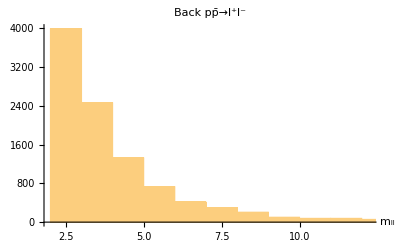

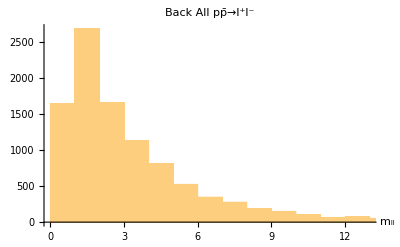

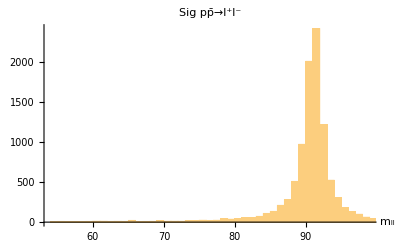

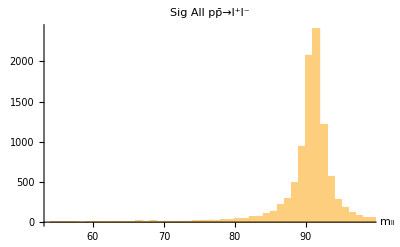

```mathematica
Histogram[InvMassLepListback,{1},PlotLabel->"Back pp̄→l^+l^-", AxesLabel->{"m_ll"}]
Histogram[InvMassLepListbackall,{1},PlotLabel->"Back All pp̄→l^+l^-", AxesLabel->{"m_ll"}]
Histogram[InvMassLepListsig,{1},PlotLabel->"Sig pp̄→l^+l^-", AxesLabel->{"m_ll"}]
Histogram[InvMassLepListsigall,{1},PlotLabel->"Sig All pp̄→l^+l^-", AxesLabel->{"m_ll"}]
```

## Cutting Data

We now implement the experimental analysis of both triggers and cuts
Event selection:
electrons must have E_T≥ 10 GeV and |η| < 2.5
muons must have  |η| < 1.3
Jet trigger: must have a jet with E_T≥ 20 GeV
Global E_T trigger: must have total of E_T≥ 50 GeV for all particles with |η| < 1.4

```mathematica
cutnames ={
"No Cuts",(*1*)
"Trigger: Electron",(*2*)
"Trigger: Muon",(*3*)
"Trigger: Jet", (*4*)
"Trigger: E_T Trigger",(*5*)
"Electron Cuts: E_T≥ 25 GeV",(*6*)
"Electron Cuts: 2 p_T≥ 7 GeV",(*7*)
"Muon Cuts: 2 p_T≥ 7 GeV "(*8*)
};
```

No create a function that implements the triggering and cuts. This function will record the number of events that pass the trigger or cut.

```mathematica
ApplyCuts[eventlist_]:=Module[{currentevent,trigger,eTrig,μTrig,electronEvent,muonEvent,jetEvent,transverseEvent,survivingevents,cutcounter,passcut
},
cutcounter=Table[0,{Length[cutnames]}];
survivingevents={};

(*run this each time we pass a cut*)
passcut[cutindex_]:=Module[{},
(*increment cut counter*)
cutcounter[[cutindex]]++;
];

For[i=1,i<(Length[eventlist]+1),i++,

(*Passcut after setting the variables*)
passcut[1];
trigger=0;

currentevent=eventlist[[i]];
electronEvent=GetParticles[currentevent,{PIDeminus,PIDeplus}];
(*Keep only electrons with |η|≤ 2.5 and Subscript[E, T]≥ 10 GeV*)
electronEvent=Select[electronEvent,((eTof[#]≥10)&&(Abs[etaOf[#]]<2.5))&];
If[Length[electronEvent]==2,
passcut[2];
trigger=1;
];

muonEvent=GetParticles[currentevent,{PIDmuminus,PIDmuplus}];
(*Keep only muons with with |η|≤ 1.3*)
muonEvent=Select[muonEvent,Abs[etaOf[#]]<1.3&];
If[Length[muonEvent]==2,
passcut[3];
trigger=1;
];

jetEvent=GetParticles[currentevent,{PIDu,PIDubar,PIDd,PIDdbar,PIDc,PIDcbar,PIDs,PIDsbar,PIDb,PIDbbar,PIDt,PIDtbar,PIDgluon}];
(*Keep only events with Jet Subscript[E, T]≥ 20 GeV with Subscript[p, T] > 0.2*)
jetEvent=Select[jetEvent,eTof[#]≥20 &];
If[Length[jetEvent]>0,
passcut[4];
trigger=1;
];

(*Keep only events with total Subscript[E, T]≥ 50 GeV for particles with |η|<1.4 *)
transverseEvent=Select[currentevent,Abs[etaOf[#]]<1.4 &];
If[Total[eT[transverseEvent]]≥ 50,
passcut[5];
trigger=1;
];


If[trigger==1, 

(* Require electron Subscript[E, T]≥ 25 GeV *)
electronEvent=Select[electronEvent,(eTof[#]≥25)&];
If[Length[electronEvent]==2,
passcut[6];
];
(* Require electron Subscript[p, T]≥ 7 GeV *)
electronEvent=Select[electronEvent,(ptOf[#]≥7)&];
If[Length[electronEvent]==2,
passcut[7];
eTrig=1;
];

(* Two muona with Subscript[p, T]≥ 7 GeV *)
If[(Length[muonEvent]==2)&&(Length[Select[muonEvent,(ptOf[#]≥7)&]]≥2),
passcut[8];
μTrig=1;
];

If[(eTrig==1)||(μTrig==1),


AppendTo[survivingevents,currentevent];
];
];
];

{cutcounter, survivingevents}
];
```

Apply cuts to the background (5/5)

```mathematica
{bkgdcutcounter,bkgdcutevents}=ApplyCuts[obkgd];
{bkgdXcutcounter,bkgdXcutevents}=ApplyCuts[obkgdX];
```

Apply cuts to signal (5/5)

```mathematica
{sigcutcounter,sigcutevents}=ApplyCuts[osig];
{sigXcutcounter,sigXcutevents}=ApplyCuts[osigX];
```

Make a table of the results
Firs for X=0
(3/3)

```mathematica
Grid[Transpose[{Prepend[cutnames,"Applied Cut"],Prepend[bkgdcutcounter,"Background"],Prepend[sigcutcounter,"Signal"]}],Frame->All,Spacings->{Automatic,1}]
```

Applied Cut | Background | Signal
No Cuts | 10000 | 10000
Trigger: Electron | 31 | 4729
Trigger: Muon | 1809 | 2700
Trigger: Jet | 0 | 0
Trigger: E_T Trigger | 2 | 5967
Electron Cuts: E_T≥ 25 GeV | 2 | 3892
Electron Cuts: 2 p_T≥ 7 GeV | 2 | 3892
Muon Cuts: 2 p_T≥ 7 GeV  | 22 | 2700

Now or X=all
(3/3)

```mathematica
Grid[Transpose[{Prepend[cutnames,"Applied Cut"],Prepend[bkgdXcutcounter,"Background"],Prepend[sigXcutcounter,"Signal"]}],Frame->All,Spacings->{Automatic,1}]
```

Applied Cut | Background | Signal
No Cuts | 10000 | 10000
Trigger: Electron | 28 | 4649
Trigger: Muon | 2230 | 2915
Trigger: Jet | 17 | 669
Trigger: E_T Trigger | 10 | 6496
Electron Cuts: E_T≥ 25 GeV | 1 | 3669
Electron Cuts: 2 p_T≥ 7 GeV | 1 | 3669
Muon Cuts: 2 p_T≥ 7 GeV  | 33 | 2915

```mathematica
MCtoExpCutlist[cutlist_,NExpBeforeCuts_]:=Module[{efficiency,NExpAfterCuts,ExpError,ExpCutsWithError},
efficiency=#/cutlist[[1]]&/@ cutlist;
NExpAfterCuts=NExpBeforeCuts*#&/@efficiency;
ExpError=NExpBeforeCuts/cutlist[[1]]*PoissonError[#]&/@cutlist;
ExpCutsWithError=Table[0,{Length[cutlist]}];
For[i=1,i<(Length[ExpCutsWithError]+1),i++,
ExpCutsWithError[[i]]=Subsuperscript[ToString[N[NExpAfterCuts[[i]]]],ToString[ExpError[[i,1]]],ToString[ExpError[[i,2]]]];
];
{ExpCutsWithError,NExpAfterCuts}
];
```

We need to combine the signal and background events from the two X cases.

```mathematica
combineError[CutsWithErr1_,CutsWithErr2_]:=Module[{combinedCuts},

combinedCuts=Table[0,{Length[CutsWithErr1]}];

For[i=1,i<(Length[CutsWithErr1]+1),i++,
combinedCuts[[i]]=ToString[ToExpression[CutsWithErr1[[i,1]]]+ToExpression[CutsWithErr2[[i,1]]] ];
];
combinedCuts
];
```

We now create the expected experimental cut list.
Directive 3: Record the integrated luminosity in inverse piccobarns (2/2)

```mathematica
Lumipb=55*10^-3;
```

```mathematica
{bkgdExpCutcounterErr,bkgdExpCutcounter}=MCtoExpCutlist[bkgdcutcounter,(σbkgd*Lumipb)];
{bkgdXExpCutcounterErr,bkgdXExpCutcounter}=MCtoExpCutlist[bkgdXcutcounter,(σbkgdX*Lumipb)];
{sigExpCutcounterErr,sigExpCutcounter}=MCtoExpCutlist[sigcutcounter,(σsig*Lumipb)];
{sigXExpCutcounterErr,sigXExpCutcounter}=MCtoExpCutlist[sigXcutcounter,(σsigX*Lumipb)];
sigoverbkgd=Table[If[bkgdExpCutcounter[[i]]+bkgdXExpCutcounter[[i]]==0,∞,(sigExpCutcounter[[i]]+sigXExpCutcounter[[i]])/(bkgdExpCutcounter[[i]]+bkgdXExpCutcounter[[i]])],{i,Length[sigExpCutcounter]}];
significance=Table[If[bkgdExpCutcounter[[i]]+bkgdXExpCutcounter[[i]]==0,∞,(sigExpCutcounter[[i]]+sigXExpCutcounter[[i]])/(√(bkgdExpCutcounter[[i]]+bkgdXExpCutcounter[[i]]))],{i,Length[sigExpCutcounter]}];
```

We can now create the Experimental cut table (3/3)

```mathematica
Grid[Transpose[{Prepend[cutnames,"Applied Cut"],Prepend[combineError[bkgdExpCutcounterErr,bkgdXExpCutcounterErr],"N_bkgd^Exp"],Prepend[combineError[sigExpCutcounterErr,sigXExpCutcounterErr],"N_sig^Exp"],Prepend[sigoverbkgd,"N_sig^Exp/N_bkgd^Exp"],Prepend[significance,"N_sig^Exp/√(N_bkgd^Exp)"]}],Frame->All,Spacings->{Automatic,1}]
```

Applied Cut | N_bkgd^Exp | N_sig^Exp | N_sig^Exp/N_bkgd^Exp | N_sig^Exp/√(N_bkgd^Exp)
No Cuts | 761.805 | 7.16595 | 0.00940654 | 0.259628
Trigger: Electron | 2.29195 | 3.36586 | 1.46856 | 2.22328
Trigger: Muon | 147.584 | 1.99639 | 0.0135271 | 0.164333
Trigger: Jet | 0.394664 | 0.191628 | 0.485549 | 0.305033
Trigger: E_T Trigger | 0.338085 | 4.42744 | 13.0957 | 7.61449
Electron Cuts: E_T≥ 25 GeV | 0.129146 | 2.72511 | 21.1011 | 7.58306
Electron Cuts: 2 p_T≥ 7 GeV | 0.129146 | 2.72511 | 21.1011 | 7.58306
Muon Cuts: 2 p_T≥ 7 GeV  | 1.93134 | 1.99639 | 1.03368 | 1.43653

Question 27: How do your total number of electron and muon signal events that pass all cuts compare to the experimental results. (2/2)
Answer 27:  We got a couple less electron events and a little more muon events.
Question 28: Can such a small number of events really indicate a discovery? Why or why not? (4/4)
Answer 28: Yes because we did have many more events, we just applied a lot of cuts. It is simply a sifting through of a lot of data.